# Position projections

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,"TwoAhead"]:=ArrayPad[rho,{{0,4},{0,4}}]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]]&[env["Unitary"][dim+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]&[env["Unitary"][dim+1]]},
Inner[Chop[#1*ApplyOperator[#2[dim+1],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*ApplyOperator[#2[Length[rho]/2+1],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,t],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,2*t],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,t],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,2*t],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
```

## Misc. functions

```mathematica
ApplyOperator[operator_?MatrixQ,rho_]:=operator.rho.ConjugateTranspose[operator]
ApplyOperator[operator_Function,rho_]:=operator[rho]
```

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=LinearModelFit[stdev,x,x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

```mathematica
DTQWSummary[coin_,env_]:=Module[{steps,probs,sds,adjst},
steps=DTQWTrace[coin,100,env];
probs=DTQWPosDistribution/@steps;
sds=DTQWPosStandardev/@probs;
adjst=DTQWSdAdjustments[sds];
GraphicsRow[{
ListLinePlot[probs[[-1]],
PlotLabel->"DTQW",
PlotRange->All,
Mesh->All
],
ListPlot[sds,
PlotLabel->adjst["BestFit"],
PlotRange->All
]
}]
]
```

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
PositionprojOperator[n_]:=Function[rho,DiagonalMatrix@Diagonal[rho]]
```

## Examples

### Position projections DTQW

```mathematica
envO0=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->False,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

```mathematica
coinO0={1,ⅈ}/Sqrt[2.];
stepsO0=DTQWTrace[coinO0,100,envO0];
```

```mathematica
(rho=stepsO0[[2]])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0.375 | 0.216506 | 0.-0.216506 ⅈ | 0.+0.375 ⅈ | 0
0 | 0.216506 | 0.125 | 0.-0.125 ⅈ | 0.+0.216506 ⅈ | 0
0 | 0.+0.216506 ⅈ | 0.+0.125 ⅈ | 0.125 | -0.216506 | 0
0 | 0.-0.375 ⅈ | 0.-0.216506 ⅈ | -0.216506 | 0.375 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

```mathematica
(rhoP=MatrixPartialTrace[rho,1,{2,3}])//MatrixForm
```

(0.125 | -0.216506 | 0
-0.216506 | 0.75 | 0.216506
0 | 0.216506 | 0.125)

```mathematica
(PositionprojOperator[1][rhoP]+rhoP)/2//MatrixForm
```

(0.125 | -0.108253 | 0.
-0.108253 | 0.75 | 0.108253
0. | 0.108253 | 0.125)

```mathematica
Inner[Chop[#1*ApplyOperator[#2[3],rhoP]]&,{0.5,0.5},{IdentityMatrix,PositionprojOperator},Plus]//MatrixForm
```

(0.125 | -0.108253 | 0
-0.108253 | 0.75 | 0.108253
0 | 0.108253 | 0.125)

### Position projections DTQW

```mathematica
envO0=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

```mathematica
coinO0={1,ⅈ}/Sqrt[2.];
AbsoluteTiming[stepsO0=DTQWTrace[coinO0,100,envO0];]
```

{0.834013,Null}

```mathematica
probsO0=DTQWPosDistribution/@stepsO0;
expvalsO0=DTQWPosExpvalue/@probsO0;
sdsO0=DTQWPosStandardev/@probsO0;
```

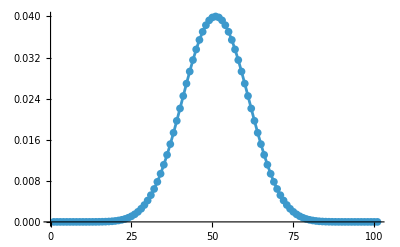

```mathematica
ListLinePlot[probsO0[[-1]],
PlotRange->All,
Mesh->All
]
```

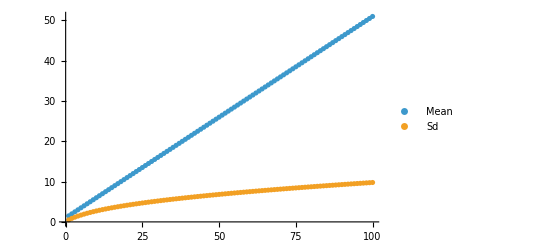

```mathematica
ListPlot[{expvalsO0,sdsO0},
PlotLegends->{"Mean","Sd"},
PlotRange->All
]
```

```mathematica
DTQWSdAdjustments[sdsO0]
```

FittedModel[…]

### More probs

#### p = 0.1

```mathematica
envO1=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.9,0.1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

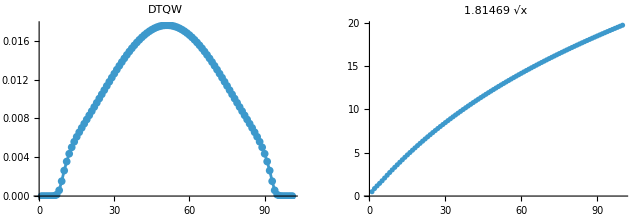

```mathematica
coinO1={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO1,envO1]
```

#### p = 0.01

```mathematica
envO2=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.99,0.01},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

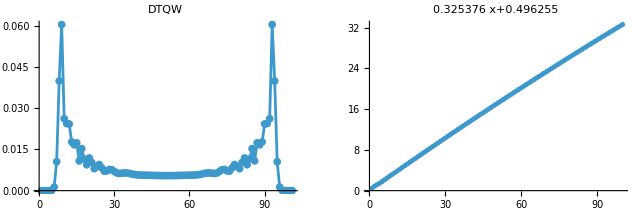

```mathematica
coinO2={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO2,envO2]
```

#### p = 0.02

```mathematica
envO3=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.98,0.02},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

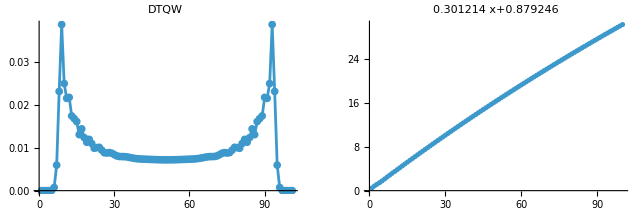

```mathematica
coinO3={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO3,envO3]
```

#### p = 0.05

```mathematica
envO4=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.95,0.05},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

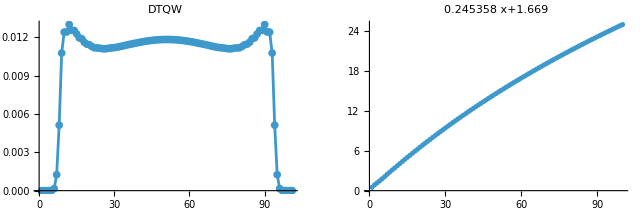

```mathematica
coinO4={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO4,envO4]
```

#### p = 0.07

```mathematica
envO5=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.93,0.07},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

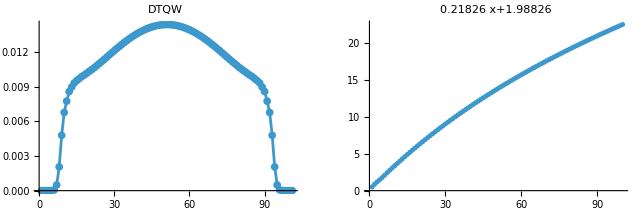

```mathematica
coinO5={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO5,envO5]
```

#### p = 1

```mathematica
envO6=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0,1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

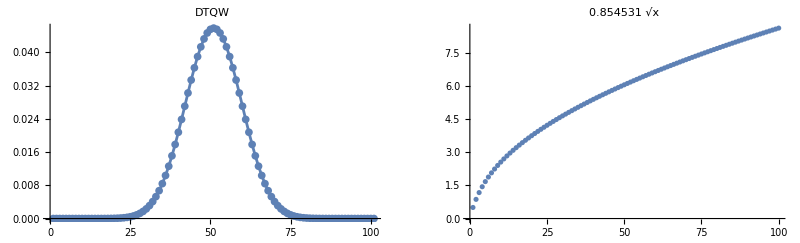

```mathematica
coinO6={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO6,envO6]
```

```mathematica
envO5[[1]]["Probabilities"]
```

{0.93,0.07}

```mathematica
ReplaceAt[{0.5,0.5}&,{1,"Probabilities"}]@(envO5/.{DTQWEnv->h})
```

ReplaceAt::reps: {0.5,0.5}& is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAt[Unevaluated[h[<|Type→ForwardGrowing,Decoherent→True,Unitary→UnitaryOperator,Probabilities→{0.93,0.07},Kraus→{IdentityMatrix[2 #1,SparseArray]&,PositionprojOperator}|>]],{0.5,0.5}&,{1,Probabilities}]

## Measuring DTQW Quanticity

```mathematica
DTQWQuanticity[coin_,range_]:=Module[{env,probs,sds,lm,nlm,p},
Table[
env=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1-p,p},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
probs=DTQWPosDistribution/@DTQWTrace[coin,100,env];
sds=DTQWPosStandardev/@probs;
lm=LinearModelFit[sds,x,x];
nlm=NonlinearModelFit[sds,A*Sqrt[x],{A},x];
{p,lm["AdjustedRSquared"],nlm["AdjustedRSquared"]},
{p,range}
]
]
```

```mathematica
coinO7={1,ⅈ}/Sqrt[2.];
desv=DTQWQuanticity[coinO7,Range[0,1,0.01]];
```

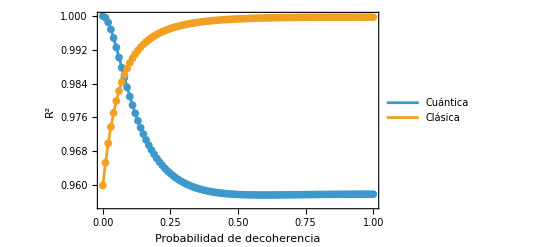

```mathematica
ListLinePlot[{#[[All,{1,2}]],#[[All,{1,3}]]}&[desv],
Frame->True,
Axes->False,
Mesh->All,
PlotLegends->{"Cuántica","Clásica"},
FrameLabel->{"Probabilidad de decoherencia","R^2"}
]
```

```mathematica
#&@desv[[All,{1,2}]]
```

{{0.07,0.987771},{0.08,0.985397},{0.09,0.983103},{0.1,0.980918}}